```mathematica
trimmedAudio =AudioTrim[CloudImport[,"Audio"],{1,45}] //AudioNormalize
```

```mathematica
trimmedAudio=AudioPan[trimmedAudio,-1]
```

```mathematica
rawAudioData = AudioData[trimmedAudio, "Real64"]
```

{{0.0000277302,0.0000163875,-0.0000188756,0.0000157723,0.0000310739,-0.0000337596,1940388,0.123801,0.102342,0.0872801,0.078405,0.0703936,0.0651376},{0.,1940398,0.}}
 |  |  |  |

```mathematica
Length@rawAudioData
```

2

```mathematica
Length@rawAudioData[[1]]
```

1940400

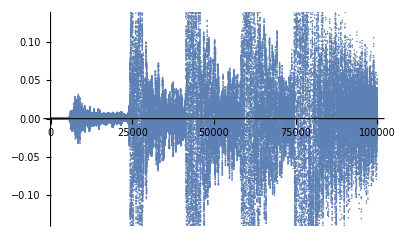

```mathematica
ListPlot@rawAudioData[[1]][[1;;100000]]
```

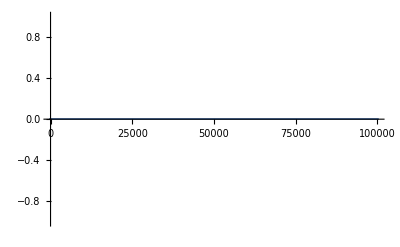

```mathematica
ListPlot@rawAudioData[[2]][[1;;100000]]
```